# PRACTICAL 13

HARIOM (20201022)

Show that ∫_C 1/(2 √z)ⅆz = 1 + i where √z is the principal branch of the square-root function and C is the line segment joining 4 to 8 + 6i. Also, plot the path of integration.

The parametrizaion of the line segment C is given by

C_1: z(t)=4 (1-t)+(8+6 ⅈ) t,0≤t≤1

The plot of the line segment C is given by the figure

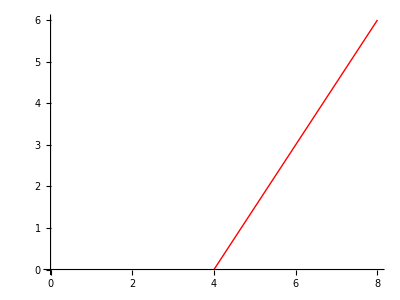

∫_C 1/(2 SqrtBox[z])ⅆz=1+ⅈ

```mathematica
w1:=4;
w2:=8+6*I;
z[t_]:=(1-t)w1+t*w2;
Print["The parametrizaion of the line segment C is given by"];
Print["C_1: z(t)=",z[t],",0≤t≤1"];
Print["The plot of the line segment C is given by the figure"]
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle->{Thick,Red},AxesOrigin->{0,0}]
f[z_]:=1/(2 √z);
Print["∫_C 1/(2 SqrtBox[z])ⅆz=",Integrate[f[z[t]]z'[t],{t,0,1}]]
```